## 500nm thick waveguide with a nanosheet capacitor

### For generating the plots in figure 2: We want the minimum sensable ΔV, the saturation voltage, and the noise as a function of ϵ/d for a reflectometer sensitivity of -120, 130, 140 dB, for 12 micron width

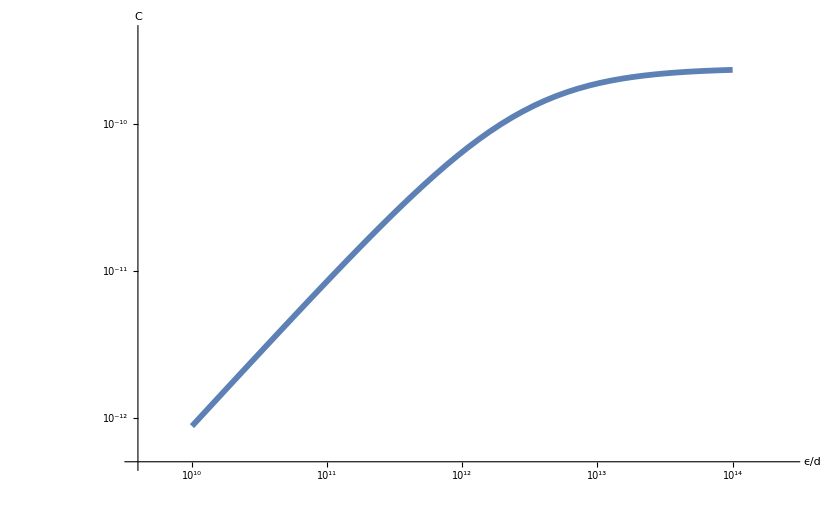

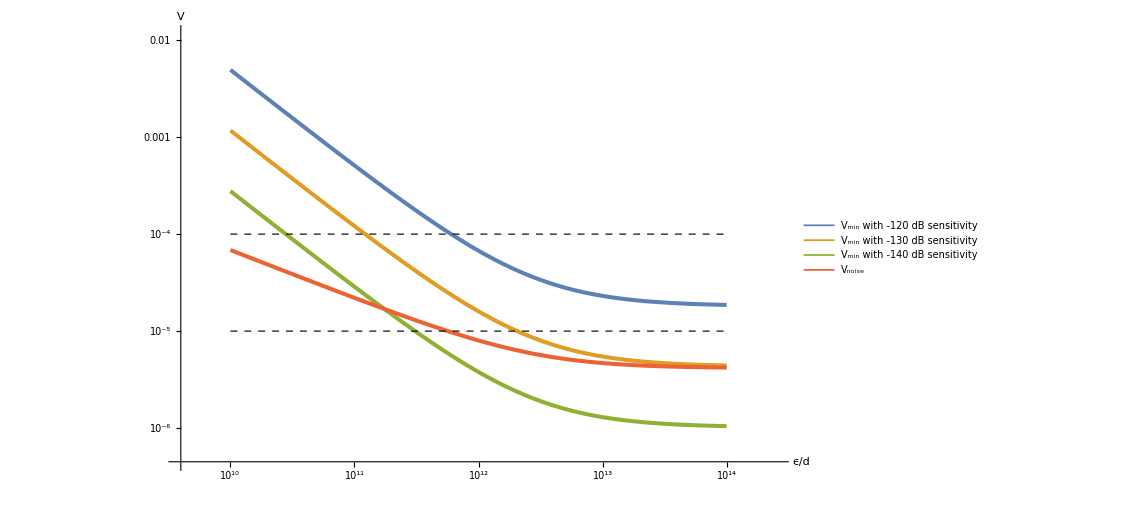

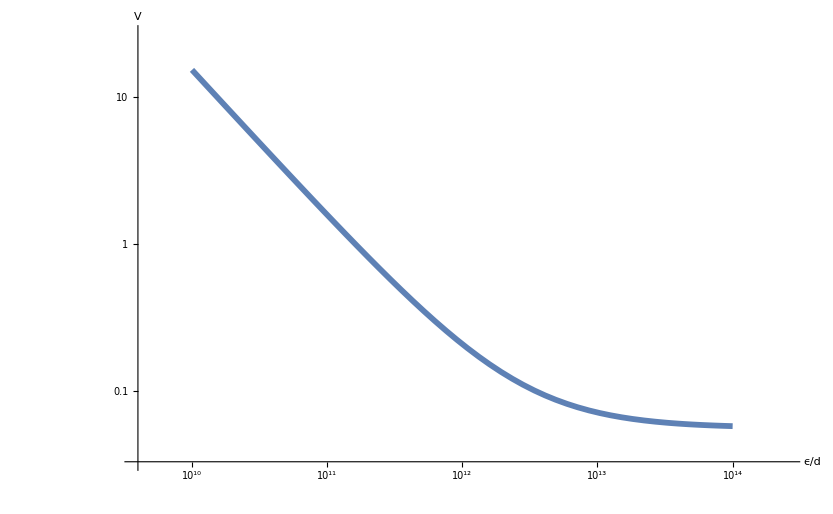

```mathematica
MinSensitivity1=-120;
MinSensitivity2=-130;
MinSensitivity3=-140;

ϵ0=8.85*10^-12;
Chcm=8.5*10^-18;(*Free dispersion coefficient for holes in silicon, from Liu 2004, in cm^2.4. The sign is unimportant.*)
Ch=Chcm*0.01^2.4; (*In meters*)
e=1.6*10^-19;
a=500*10^-9; (*Thickness of the waveguide in meters*)
L=20*10^-6; (*length of the sensing region in meters*)
w=500*10^-9;(*Width of the waveguide in meters*)
wfiber=12*10^-6;(*Width of the fiber*)
dep=7*10^-6;(*thickness of outer conductor in meters*)
dmetal=500*10^-9; (*width of metal*)

(*Now calculate change in effective refractive index:*)

A=w*L; (*Area of the nanosheet capacitor*)
(*Insulating Cap: ϵ0 ϵ A/d*)
InsulatingCap=ϵ0 A ϵoverd;
(*Interface Cap*)
InterfaceCap=1*wfiber*L//N;(*1 farad per square meter capacitance at fiber surface*)
Cap=1/(1/InsulatingCap+1/InterfaceCap); (*Effective capacitance*)
(*Refractive Index Change*)
Δneff=Ch 0.01/a(Cap/(e A)ΔV)^0.8;

(*Calculate Reflections*)
n=3;
R=(Δneff/(2n))^2;
(*Decibels:*)
10 Log10[R];

(*Now, solve for ΔV as a function of ϵoverd*)
SolveRule1=First[Solve[MinSensitivity1==10 Log10[R],ΔV]];
SolveRule2=First[Solve[MinSensitivity2==10 Log10[R],ΔV]];
SolveRule3=First[Solve[MinSensitivity3==10 Log10[R],ΔV]];

(*We now calculate noise*)
T=300;
kB=1.38*10^-23;
Vrms=√(kB T /Cap);
(*To get the RC time constant:*)
TotalL=50*10^-2;
ρmetal=100*10^-9;
RGround=(ρmetal*TotalL)/(wfiber*dmetal)//N;
RGround*Cap;
(*To get dynamic range, i.e., this is the saturation voltage*)
VolOfOuterConductor=wfiber*L*dep;
Δc=5*10^22;(*per cubic meter*)
SaturationVoltage=(VolOfOuterConductor*Δc*e)/Cap;

LogLogPlot[Cap,{ϵoverd,10^10,10^14},AxesLabel->{"ϵ/d","C"},AxesStyle->Large,PlotStyle->Thickness[.005]]
(*LogLogPlot[{ΔV/.SolveRule1,ΔV/.SolveRule2,ΔV/.SolveRule3,SaturationVoltage,Vrms,10^-5},{ϵoverd,10^11,10^14},AxesLabel->{"ϵ/d","V"},AxesStyle->Large,PlotStyle->{Thickness[.0035],Thickness[.0035],Thickness[.0035],Thickness[.0035],Thickness[.0035],Thickness[.002]},PlotLegends->Placed[{"Voltage sensed at -120 dB","Voltage sensed at -130 dB","Voltage sensed at -140 dB","V_sat","V_noise"},{0.9,0.9}]]*)
LogLogPlot[{ΔV/.SolveRule1,ΔV/.SolveRule2,ΔV/.SolveRule3,Vrms,10^-5,10^-4},{ϵoverd,10^10,10^14},AxesLabel->{"ϵ/d","V"},AxesStyle->Large,PlotStyle->{Thickness[.0035],Thickness[.0035],Thickness[.0035],Thickness[.0035],{Thickness[.001],Dashed,Black},{Thickness[.001],Dashed,Black}},PlotLegends->Placed[{"V_min with -120 dB sensitivity","V_min with -130 dB sensitivity","V_min with -140 dB sensitivity","V_noise"},{0.9,0.9}]]
LogLogPlot[SaturationVoltage,{ϵoverd,10^10,10^14},AxesLabel->{"ϵ/d","V"},AxesStyle->Large,PlotStyle->Thickness[.005]]
```

### Plot of electric field enhancement factor for 100 uV.

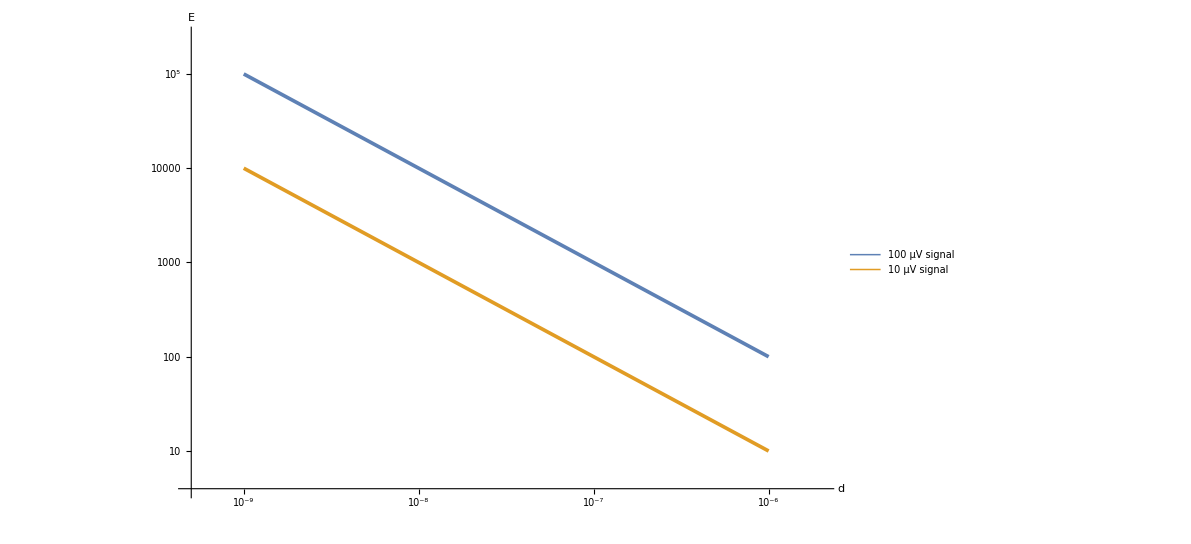

```mathematica
LogLogPlot[{10^-4/x,10^-5/x},{x,10^-6,10^-9},AxesLabel->{"d","E"},AxesStyle->Large,PlotStyle->Thickness[0.003],PlotLegends->Placed[{"100 μV signal","10 μV signal"},{.9,.9}]]
```

```mathematica
_
```